```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = Import["s_Distributions_LKJ.csv"][[2;;]];
mData = ArrayReshape[#,{4,4}]&/@data;
```

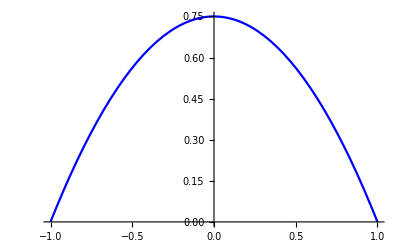

```mathematica
Plot[PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[2,2]],x],{x,-1,1},PlotStyle->Blue]
```

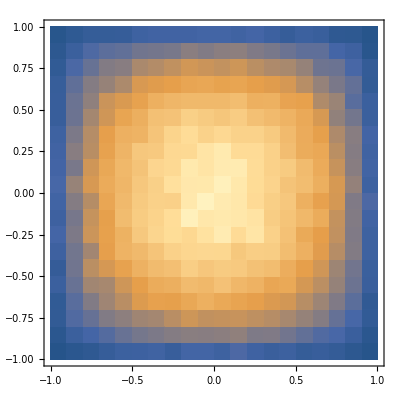

```mathematica
DensityHistogram[Thread[{mData[[All,1,2]],mData[[All,1,3]]}]]
```

```mathematica
ListContourPlot[Thread[{mData[[All,1,2]],mData[[All,1,3]]}]]
```